“Algorithms for Group 2” / UD RC11 - UCL Bartlett 
05 12 2019
Philippe Morel

PART 1

1)
Let us start with the pseudocode on slide 36.
I am not sure I understand everything, and most of all I don’t have the input data at the moment (the set of land plots) to compute the areas.
But it’s not a problem!
Let’s consider “ideal” inputs for the moment:

(Let us first assign a global value for the size of the future graphics/images)

```mathematica
imageSizeValue=600
```

600

Let’s define a small function for future (fake) generic land plots, with areas between 500 and 1500m2:

```mathematica
fakeLandPlot:=RandomReal[{250,1500}]
```

Let’s create a set of 400 random points in an area of 1000 x 1000m (1 million m2 = 1 km2 ; a district of 1x1 km in a city).
These random points are considered here as centers of gravity of the land plots (the future input data) you have to analyse.

```mathematica
pointCoordinateFunction:={RandomReal[{-5000,5000}],RandomReal[{-5000,5000}]}
```

```mathematica
pointCoordinateList=Table[pointCoordinateFunction,400];
```

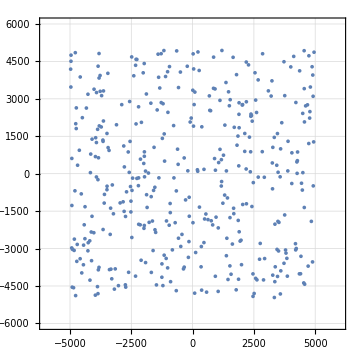

```mathematica
pointsPlot=ListPlot[pointCoordinateList,Frame->True,PlotRange->{{-6000,6000},{-6000,6000}},GridLines->Automatic,AspectRatio->1,ImageSize->Medium]
```

Let’s assign an area to each of these points (again, here we create the data but in the future you’ll get the data from the cities):

```mathematica
pointCoordinateListWithAreas=Map[{#,fakeLandPlot}&,pointCoordinateList];
```

And create squares (the land plots) whose areas are defined by second elements in the list “pointCoordinateListWithAreas”.
Let’s also create a small function for that:

```mathematica
mySquarePlotsFunction[{{x_,y_},area_}]:=Rectangle[{x,y},{x+Sqrt[area],y+Sqrt[area]}]
```

I select the lands whose areas are equal or greater than 1000m2, and put the other ones in another category (another set, or another list)

```mathematica
mySquareOK=Select[pointCoordinateListWithAreas,#[[2]]≥1000&];
mySquareTooSmall=Complement[pointCoordinateListWithAreas,mySquareOK];
mySquareOK//Length
mySquareTooSmall//Length
```

151

249

As you can see we have land plots of which areas are ok, and others which are too small...
So we now print 400m radius circles around the centers of the land plots that are ok, in order to determine their price for future steps

```mathematica
mySquareOKList=mySquarePlotsFunction/@mySquareOK;
mySquareTooSmallList=mySquarePlotsFunction/@mySquareTooSmall;
```

```mathematica
squarePlot=Graphics[{mySquareOKList,mySquareTooSmallList},Frame->True,PlotRange->{{-6000,6000},{-6000,6000}},GridLines->Automatic,AspectRatio->1,ImageSize->Medium];
circlesPlot=Graphics[Circle[#,400]&/@(First/@mySquareOK)];
```

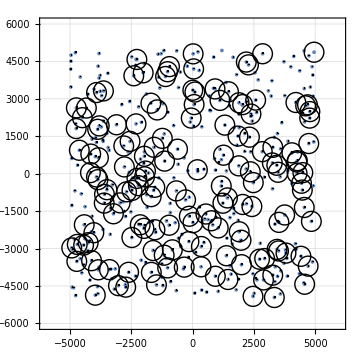

```mathematica
Show[{pointsPlot,squarePlot,circlesPlot},ImageSize->Medium,AspectRatio->1]
```

I can zoom in on a smaller area of the district.
Later we’ll be able to give colors (and any other features) to the squares that are ok, after the analysis of the immediate neighbourhood inside the circle):

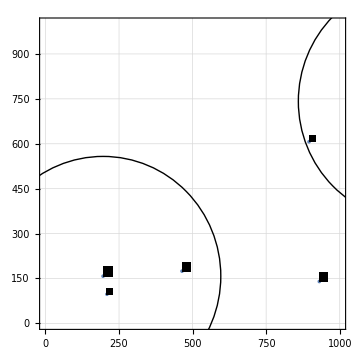

```mathematica
Show[{pointsPlot,squarePlot,circlesPlot},PlotRange->{{0,1000},{0,1000}},ImageSize->Medium,AspectRatio->1]
```

```mathematica
Names["Global`*"]
```

{a,allFacilitiesList,allFacilitiesPlot,allPlotForNextStep,area,args,b,busStationList,circlesPlot,circlesPlotWithPrice,dims,fakeLandPlot,gymList,hospitalList,i,imageSizeValue,list,listOfCouples,listOfCouplesOK,listOfNorms,listOfWeights,list$,mySquareOK,mySquareOKCenter,mySquareOKList,mySquarePlotsFunction,mySquareTooSmall,mySquareTooSmallList,nurseryList,parkList,pointCoordinateFunction,pointCoordinateList,pointCoordinateListWithAreas,pointsPlot,primarySchoolList,socialCultureList,squarePlot,supermarketList,trajectoryPlotOk,undergroundStationList,x,x1,x2,y,y1,y2}

2)
We have written a couple of very simple functions to generate and select pieces of land based on their areas.
Now let’s define a couple of functions for the analysis of the elements who are (or not) inside the circles:

	- Underground station ; US
	- Bus station ; BS
	- Supermarket ; S
	- Social-culture facilities ; SC
	- Gym ;
	- Primary school ; PS
	- Nursery ; N
	- Hospital ; H
	- Park ; P

For that we’ll simply generate lists of random points within our initial study area by making use of the function “pointCoordinateFunction”:

```mathematica
undergroundStationList=Table[pointCoordinateFunction,5];
busStationList=Table[pointCoordinateFunction,20];
supermarketList=Table[pointCoordinateFunction,10];
socialCultureList=Table[pointCoordinateFunction,10];
gymList=Table[pointCoordinateFunction,4];
primarySchoolList=Table[pointCoordinateFunction,8];
nurseryList=Table[pointCoordinateFunction,8];
hospitalList=Table[pointCoordinateFunction,2];
parkList=Table[pointCoordinateFunction,4];

allFacilitiesList=Join[undergroundStationList,busStationList,supermarketList,socialCultureList,gymList,primarySchoolList,nurseryList,hospitalList,parkList];
```

```mathematica
allFacilitiesPlot=Graphics[{{Magenta,Point[#]}&/@undergroundStationList,{Gray,Point[#]}&/@busStationList,{Brown,Point[#]}&/@supermarketList,{Blue,Point[#]}&/@socialCultureList,{Purple,Point[#]}&/@gymList,{Pink,Point[#]}&/@primarySchoolList,{Orange,Point[#]}&/@nurseryList,{Red,Point[#]}&/@hospitalList,{Green,Point[#]}&/@parkList}];
```

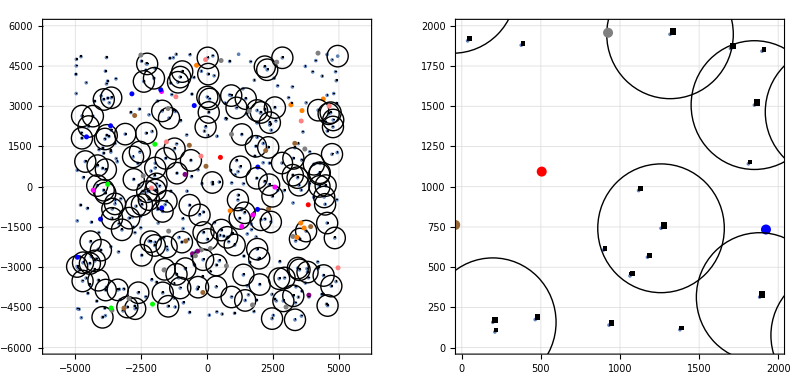

```mathematica
GraphicsGrid[{{allPlotForNextStep=Show[{pointsPlot,squarePlot,circlesPlot,(allFacilitiesPlot/.Point[list_]:>{PointSize[0.01],Point[list]})},AspectRatio->1], Show[{pointsPlot,squarePlot,circlesPlot,(allFacilitiesPlot/.Point[list_]:>{PointSize[0.02],Point[list]})},PlotStyle->Directive[PointSize[5]],
PlotRange->{{0,2000},{0,2000}},AspectRatio->1]}},ImageSize->800]
```

What we have to do now is to check, for each land plot whose area is OK, how many facilities are within a radius of 400m.
(This is what you wrote in pseudocode)
So for each element in the list “mySquareOK”, we’ll check if facilities are present around.

```mathematica
mySquareOK//Short
```

{{{2039.86,2768.74},1066.06},«149»,{{2280.39,4361.55},1001.88}}

```mathematica
mySquareOKCenter=mySquareOK/.{a_,b_}->a;
```

```mathematica
listOfCouples=Table[{mySquareOKCenter[[i]],#}&/@allFacilitiesList,{i,1,Length[mySquareOKCenter]}];
listOfCouplesOK=Select[#,Norm[#[[2]]-#[[1]]]<400&]&/@listOfCouples;
trajectoryPlotOk=Graphics[Line/@Flatten[listOfCouplesOK,1]];
listOfNorms=listOfCouplesOK/.{{x1_?NumberQ,y1_?NumberQ},{x2_?NumberQ,y2_?NumberQ}}-> Norm[{x2,y2}-{x1,y1}];
```

```mathematica
listOfWeights=Length/@listOfNorms
Max[listOfWeights]
listOfWeights//Length
mySquareOK//Length
```

{0,0,0,0,0,1,0,0,0,0,0,3,1,0,0,0,1,0,0,1,1,0,1,0,0,1,1,1,0,1,0,0,1,0,1,0,1,1,0,0,2,1,0,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,0,0,0,0,0,2,0,0,0,1,0,0,0,1,2,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,3,0,0,1,0,0,1,0,0,0,2,0,0,1,0,1,0,1,0,0,0,0,0,1,0,0,0,1,0,0,1,1,0,0,0,1,0,0,0}

3

151

151

```mathematica
Position[listOfWeights,0]
Position[listOfWeights,1]
Position[listOfWeights,2]
```

{{1},{2},{3},{4},{5},{7},{8},{9},{10},{11},{14},{15},{16},{18},{19},{22},{24},{25},{29},{31},{32},{34},{36},{39},{40},{43},{45},{46},{47},{48},{49},{50},{51},{52},{53},{56},{57},{58},{59},{60},{61},{63},{64},{65},{66},{67},{69},{70},{71},{73},{74},{75},{78},{80},{81},{82},{83},{84},{85},{86},{87},{88},{89},{90},{91},{92},{93},{94},{95},{96},{98},{99},{100},{101},{102},{103},{105},{106},{107},{108},{109},{110},{111},{112},{114},{115},{117},{118},{120},{121},{122},{124},{125},{127},{129},{131},{132},{133},{134},{135},{137},{138},{139},{141},{142},{145},{146},{147},{149},{150},{151}}

{{6},{13},{17},{20},{21},{23},{26},{27},{28},{30},{33},{35},{37},{38},{42},{44},{54},{55},{62},{72},{76},{79},{97},{104},{116},{119},{126},{128},{130},{136},{140},{143},{144},{148}}

{{41},{68},{77},{123}}

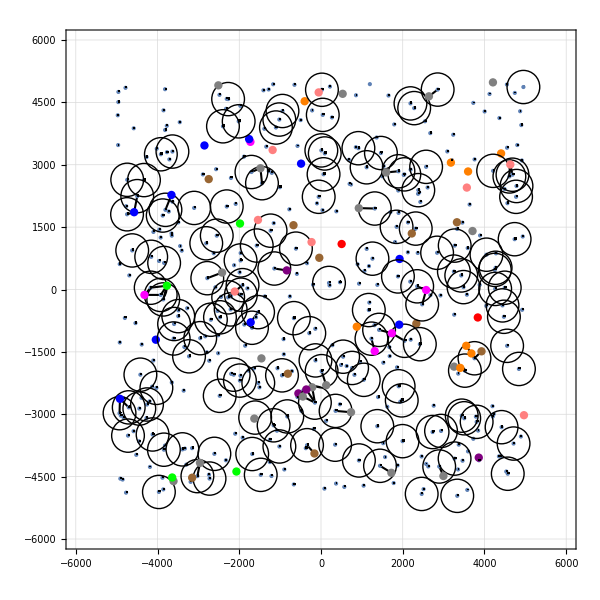

```mathematica
Show[{trajectoryPlotOk/.Line[list_]:>{Thickness[0.0025],Line[list]},Show[{pointsPlot/.Point[list_]:>{PointSize[0.005],Point[list]},squarePlot,circlesPlot,(allFacilitiesPlot/.Point[list_]:>{PointSize[0.01],Point[list]})},AspectRatio->1]},Frame->True,PlotRange->{{-6000,6000},{-6000,6000}},GridLines->Automatic,AspectRatio->1,ImageSize->600]
```

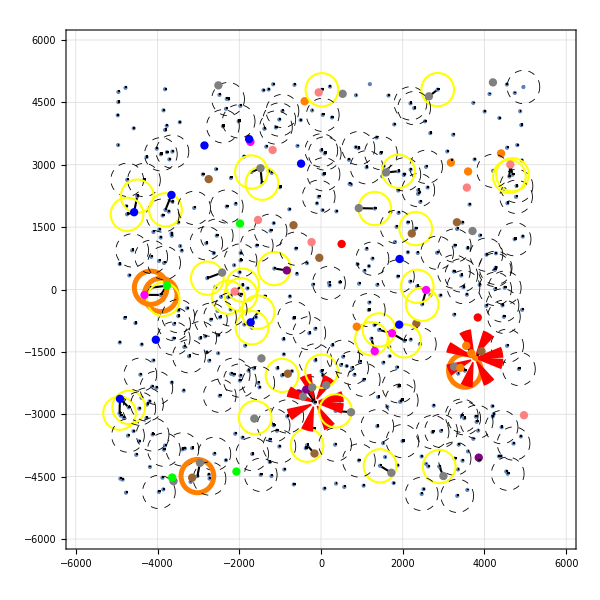

```mathematica
circlesPlotWithPrice=Graphics[Thread[List[listOfWeights,circlesPlot[[1]]]]/.{0?IntegerQ->Sequence[Dashed,Thickness[0.001]],1?IntegerQ->Sequence[Yellow,Thickness[0.0025]],2?IntegerQ->Sequence[Orange,Thickness[0.006]],3?IntegerQ->Sequence[Red,Thickness[0.03],Dashed],4?IntegerQ->Sequence[Red,Thickness[0.05],Dashed]}];

Show[{trajectoryPlotOk/.Line[list_]:>{Thickness[0.0025],Line[list]},Show[{pointsPlot/.Point[list_]:>{PointSize[0.005],Point[list]},squarePlot,circlesPlotWithPrice,(allFacilitiesPlot/.Point[list_]:>{PointSize[0.01],Point[list]})},AspectRatio->1]},Frame->True,PlotRange->{{-6000,6000},{-6000,6000}},GridLines->Automatic,AspectRatio->1,ImageSize->600]
```

At that moment we have a list of land plots who are OK (“mySquareOK”) and a list of their weights (“listOfWeights”) which in fact, before we apply more subtle weighting coefficients, will give you the price.
In your formula on slide 36, V(x)=15%*value US(x) + 15%*value BS(x) + 10%* value S(x)... These percentages are in fact weighting coefficients of 0.15, 0.15, 0.10 etc.
Let’s skip this for the moment as it will be so easy to do.

3)
Let’s jump to slide 45 and define basic functions for it.
BTW I am not sure about the meaning you give to the name “factorial structure” !
Explain me...
 
 Variables names (never start with capital letters as MMA built-in functions do have capital them):

	- Size: size
	- Type: type
	- Bedrooms: bedroom
	- Working Space: workingSpace
	- Kitchen: kitchen
	- Laundry room: laundryRoom
	- Dining room: diningRoom
	- ...
	
All the parameters (including the definition of what is private and what is shared) you want to define have numeric values. They will be either defining quantities (area, repetition, rate, etc.), or qualities (topology)
I let you write the code for slides 45 to 48 because this is easy (if you don’t manage to make it i’ll help you of course)

Let’s say that your housing unit (the main component, including shared/non shared workspaces, etc., will be represented by a vector like this: {{1.22, 4.56, 5.31},{1,4,2,1},{0,0,0,1,0}...}
First a list of real values, then a couple of integers, then boolean variables. It could be for defining: {areas, distances, ...}, {number of kids, number of rooms, ...}, {presence/absence of something, connected/not connected, ...}.

What you have to do now is to write a couples of lines and loops for pages 45 to 48 and make sure that you will have outputs with shape {{1.22, 4.56, 5.31},{1,4,2,1},{0,0,0,1,0}...} you will be able to put and export as Excel files, then you will simply have to importe this in Rhino and it will be done :)

I let you work before moving to PART 2 and more, so that I also dedicate time to the other groups